# N -> nu γ* -> nu e+e-

```mathematica
<<FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/matheushostert/Repos/stdHNL/calculations

## Constants

```mathematica
dm[mu_]:=GA[mu]
dm[5]:=DiracMatrix[5]
ds[p_]:=DiracSlash[p]
mt[mu_,nu_]:=MetricTensor[mu,nu]
fv[p_,mu_]:=FourVector[p,mu]
epsilon[a_,b_,c_,d_]:=LeviCivita[a,b,c,d]
id[n_]:=IdentityMatrix[n]
sp[p_,q_]:=ScalarProduct[p,q]
li[mu_]:=LorentzIndex[mu]
prop[p_,m_]:=ds[p]+m
PR=dm[6];
PL=dm[7];
dσ[μ_,ν_]:=I/2(dm[μ].dm[ν]-dm[ν].dm[μ]);
SetOptions[{DiracMatrix, DiracSlash,LeviCivita, FourVector, MetricTensor, SetMandelstam, OneLoop, ScalarProduct},Dimension->4];
```

## Kinematics

```mathematica
Lambda[a_,b_, c_] := (a-b-c)^2-4b c
subP = {Pair[Momentum[k1],Momentum[k1]]-> m1^2,
Pair[Momentum[k2],Momentum[k2]]->m2^2,
Pair[Momentum[k3],Momentum[k3]]->m3^2,
Pair[Momentum[k4],Momentum[k4]]->m4^2,
Pair[Momentum[k1],Momentum[k2]]->(-m34sqr+m1^2+m2^2)/2,
Pair[Momentum[k1],Momentum[k3]]->-1/2(m24sqr - m1^2-m3^2),
Pair[Momentum[k1],Momentum[k4]]->(-m23sqr+m1^2+m4^2)/2,
Pair[Momentum[k2],Momentum[k3]]->(m23sqr-m2^2-m3^2)/2,
Pair[Momentum[k2],Momentum[k4]]->(m24sqr-m4^2-m2^2)/2,
Pair[Momentum[k3],Momentum[k4]]->(m34sqr-m4^2-m3^2)/2,
Pair[Momentum[s],Momentum[s]]-> -1,
Pair[Momentum[k1],Momentum[s]]-> 0,
Pair[Momentum[k2],Momentum[s]]-> k3CM*c3+k4CM*c4,
Pair[Momentum[k3],Momentum[s]]-> -k3CM *c3,
Pair[Momentum[k4],Momentum[s]]-> -k4CM*c4};

subPexpressions={
k4CM->m1/2 √Lambda[1,m23sqr/m1^2,m4^2/m1^2],k3CM->m1/2 √Lambda[1,m24sqr/m1^2,m3^2/m1^2],
k2CM->m1/2 √Lambda[1,m34sqr/m1^2,m2^2/m1^2]};

subEexpressions={
E4CM->(m1^2+m4^2-m23sqr)/(2m1),E3CM->(m1^2+m3^2-m24sqr)/(2m1),
E2CM->(m1^2+m2^2-m34sqr)/(2m1)};

subC4expressions={c4-> c3*c34-√(1-c3*c3)*√(1-c34*c34)*cphi34};

subC34expressions={c34-> (m23sqr+m24sqr-m2*m2-m1*m1+2*E3CM*E4CM)/(2*k3CM*k4CM)};

subMassNorm ={m1-> 1  m1,m2-> x2 m1, m3-> x3 m1, m4 -> x4 m1, m24sqr-> x24 m1^2,m23sqr-> x23 m1^2, m34sqr-> x34 m1^2,MW-> xWBOSON m1,MZBOSON-> xZBOSON m1, MZPRIME-> xZPRIME m1};
```

## Phase space

```mathematica
PS3 = 1/(32 m1^2 (2 π)^5);
FluxFactor=1/(2 m1);
SpinAverage = 1/2;
```

### Substitute in the special cases

```mathematica
subMasslessNorm={x2-> 0, x3->0,x4-> 0};
subMassless={m1-> mh,m2-> 0, m3->0,m4-> 0};
subGf={gweak-> √((8 Gf MW^2)/(√2))};
subAlphaQED={eQED-> √(alphaQED*4π)};
subINTEGRATION={m34sqr-> m1^2+m2^2+m3^2+m4^2-m24sqr-m23sqr };
subgLgR=(Solve[Ca== gL-gR&&Cv==gL+gR,{gL,gR}])[[1]];
subCvCa={Ca-> -1/2,Cv-> (-1/2+2 Sin[W]^2)};
subCW=(Solve[Gf/(√2)-gweak^2/(8 cw^2 MZBOSON^2)==0,{cw}]//Simplify//PowerExpand)[[1]];
submasses={m1-> mh,m4-> 0,m3-> mlep, m2-> mlep};
```

## Amplitudes

## ν_h (k1) -->l_β-(k2) l_α+(k3) v_i (k4)

```mathematica
MajAmp=-eQED* dij *2* SpinorUBar[k4,m4] .(dσ[μ,γ].fv[k1-k4,γ]).PL.((1+h dm[5]. ds[s])/2).SpinorU[k1,m1] * SpinorUBar[k2,m2].dm[ν].SpinorV[k3,m3]*(mt[μ,ν]/(Pair[Momentum[k3+k2],Momentum[k2+k3]]));
```

```mathematica
MajAmpC =-eQED* dij *2*-I/2 ComplexConjugate[SpinorUBar[k4,m4] .(dm[μ].dm[γ]-dm[γ].dm[μ]).fv[k1-k4,γ].PL.((1+h dm[5]. ds[s])/2).SpinorU[k1,m1]]*(mt[μ,ν]/(Pair[Momentum[k3+k2],Momentum[k3+k2]]))ComplexConjugate[SpinorUBar[k2,m2].dm[ν].SpinorV[k3,m3]]/.{μ-> μ2,ν-> ν2};
```

```mathematica
(*MajAmp=-eQED* dij *2* SpinorUBar[k4,m4] .(dσ[μ,γ].fv[k1-k4,γ]).PL.SpinorU[k1,m1] * SpinorUBar[k2,m2].dm[ν].SpinorV[k3,m3]*mt[μ,ν]/(Pair[Momentum[k3+k2],Momentum[k2+k3]]);*)
```

```mathematica
(*MajAmpC =-eQED* dij *2*-I/2 ComplexConjugate[SpinorUBar[k4,m4] .(dm[μ].dm[γ]-dm[γ].dm[μ]).fv[k1-k4,γ].PL.SpinorU[k1,m1]]*mt[μ,ν]/(Pair[Momentum[k3+k2],Momentum[k3+k2]])ComplexConjugate[SpinorUBar[k2,m2].dm[ν].SpinorV[k3,m3]]/.{μ-> μ2,ν-> ν2};*)
```

## Spin sums and Trace

```mathematica
MajAmpSQR = FermionSpinSum[MajAmpC MajAmp]//Simplify
```

1/(4 (OverBar[k2]+OverBar[k3])^4)dij^2 eQED^2 (ḡ)^μν (ḡ)^μ2ν2 (OverBar[k1]-OverBar[k4])^γ (OverBar[k1]-OverBar[k4])^($AL($4733)) tr((γ̄·OverBar[k2]+m2).(γ̄)^ν.(γ̄·OverBar[k3]-m3).(γ̄)^ν2) tr((γ̄·OverBar[k1]+m1).(1-h (γ̄·s̄).(γ̄)^5).(γ̄)^6.((γ̄)^($AL($4733)).(γ̄)^μ2-(γ̄)^μ2.(γ̄)^($AL($4733))).(γ̄·OverBar[k4]+m4).((γ̄)^μ.(γ̄)^γ-(γ̄)^γ.(γ̄)^μ).(γ̄)^7.(h (γ̄)^5.(γ̄·s̄)+1))

```mathematica
TracedMajAmpSQR = ((MajAmpSQR/.{DiracTrace-> Tr}/.{k4-> k1 -k2-k3}//Contract)//Simplify)/.h^2-> 1;
TracedMajAmpSQRsummed =( (TracedMajAmpSQR/.h-> 1)+(TracedMajAmpSQR/. h-> -1)//FullSimplify)/.h^2-> 1;
```

```mathematica
(*TracedMajAmpSQR = (MajAmpSQR/.{DiracTrace-> Tr}/.{k4-> k1 -k2-k3}//Contract)//Simplify;*)
(*TracedMajAmpSQRsummed =( TracedMajAmpSQR//FullSimplify)*)
```

## Full Expression

```mathematica
FULL = TracedMajAmpSQR* PS3*FluxFactor*4 π^2*2*SpinAverage/.subP/.subPexpressions/.subINTEGRATION//ExpandAll//Cancel//Simplify;
FULLAVE = TracedMajAmpSQRsummed* PS3*FluxFactor*4 π^2*2*SpinAverage/.subP/.subPexpressions/.subINTEGRATION//ExpandAll//Cancel//Simplify;
```

```mathematica
Needs["ToPython`"]
```

```mathematica
Export["N_to_nu_ee_dipole.dat",ToPython[FULLAVE/.{m1-> mh,m4-> mf,m2-> mm, m4-> mp,m24sqr-> u,m23sqr-> t},"np"]]
```

N_to_nu_ee_dipole.dat

## Further Analytical Manipulations

```mathematica
dGammaHelMassless= FULLAVE/.subMassless/.subAlphaQED/.{m24sqr-> u,m23sqr-> t}//Simplify//PowerExpand
dGammaHel= FULLAVE/.submasses/.subAlphaQED/.{m24sqr-> u,m23sqr-> t}//Simplify//PowerExpand
```

(alphaQED dij^2 (-mh^2 (t+2 u)+mh^4+2 u (t+u)))/(8 π^2 mh^3 t)

(alphaQED dij^2 (mh^4 (2 mlep^2+t)-mh^2 t (t+2 u)-2 t (mlep^2-u) (-mlep^2+t+u)))/(8 π^2 mh^3 t^2)

### d Gamma / dE+ dE-

```mathematica
DGammaDeDe=Integrate[Integrate[(((dGammaHelMassless/(2π*2)*4 mh^2/.subC4expressions//Simplify)/.subC34expressions)//Simplify)/.subEexpressions/.subPexpressions/.{cphi34-> Cos[phi34]}//FullSimplify,{phi34,0,2π}],{c3,-1,1}]/.{u-> mh^2-2 mh Eminus,t->- mh^2 + 2mh (Eplus+Eminus) }/.subEexpressions//FullSimplify
```

(alphaQED dij^2 (mh (Eminus+Eplus)-4 Eminus Eplus))/(π^2 (2 (Eminus+Eplus)-mh))

```mathematica
DGammaDeDeMass=Integrate[Integrate[(((dGammaHelMassless/(2π*2)*4 mh^2/.subC4expressions//Simplify)/.subC34expressions)//Simplify)/.subEexpressions/.subPexpressions/.{cphi34-> Cos[phi34]}//FullSimplify,{phi34,0,2π}],{c3,-1,1}]/.{u-> mh^2-2 mh Eminus,t->- mh^2 + 2mh (Eplus+Eminus) }/.subEexpressions//FullSimplify
```

(alphaQED dij^2 (mh (Eminus+Eplus)-4 Eminus Eplus))/(π^2 (2 (Eminus+Eplus)-mh))

```mathematica
DoubleDiff[Eminus_,Eplus_]:=Evaluate[DGammaDeDe/.{alphaQED-> 1,dij-> 1,mh-> 1}]
```

```mathematica
Plot3D[DoubleDiff[x,y],{x,0.5,1},{y,0.5,1},PlotLegends->Automatic]
```

-Graphics3D-

### Total rate -- Integration over t and u

```mathematica
E2 =(t-m3^2+m2^2)/(2 √t);E4 =(m1^2-t-m4^2)/(2 √t);P2 = √(E2^2-m2^2);P4 = √(E4^2-m4^2);
umax= (E2+E4)^2-(P2-P4)^2/.submasses//Simplify
umin =(E2+E4)^2-(P2+P4)^2/.submasses//Simplify
```

1/2 (√(((t-mh^2)^2)/t) √(t-4 mlep^2)+mh^2+2 mlep^2-t)

1/2 (-√(((t-mh^2)^2)/t) √(t-4 mlep^2)+mh^2+2 mlep^2-t)

### d Gamma / du dt

```mathematica
dGammadudtMassless = Integrate[Integrate[(((dGammaHelMassless/(2π*2)/.subC4expressions//Simplify)/.subC34expressions)//Simplify)/.subEexpressions/.subPexpressions/.{m24sqr-> u,m23sqr-> t}/.{cphi34-> Cos[phi34]}//FullSimplify,{phi34,0,2π}],{c3,-1,1}]//FullSimplify
dGammadudt = Integrate[Integrate[(((dGammaHel/(2π*2)/.subC4expressions//Simplify)/.subC34expressions)//Simplify)/.subEexpressions/.subPexpressions/.{m24sqr-> u,m23sqr-> t}/.{cphi34-> Cos[phi34]}//FullSimplify,{phi34,0,2π}],{c3,-1,1}]//FullSimplify
```

(alphaQED dij^2 (-mh^2 (t+2 u)+mh^4+2 u (t+u)))/(8 π^2 mh^3 t)

(alphaQED dij^2 (mh^4 (2 mlep^2+t)-mh^2 t (t+2 u)-2 t (mlep^2-u) (-mlep^2+t+u)))/(8 π^2 mh^3 t^2)

### d Gamma/ dt

```mathematica
dGammadtMassless=Simplify[Integrate[dGammadudtMassless,{u,myumin,myumax},Assumptions->{myumax>myumin&&myumin>0&&m1> 0&&t<myumax&&t>myumin&&t<m1^2}]/.myumin-> umin/.myumax-> umax/.{mlep-> 0}//Simplify,Assumptions->{0<t<mh^2}]
dGammadt=Simplify[Integrate[dGammadudt,{u,myumin,myumax},Assumptions->{myumax>myumin&&myumin>0&&m1> 0&&t<myumax&&t>myumin&&t<m1^2}]/.myumin-> umin/.myumax-> umax//Simplify,Assumptions->{0<t<mh^2}]
```

(alphaQED dij^2 (mh^2-t)^2 (2 mh^2+t))/(24 π^2 mh^3 t)

(alphaQED dij^2 (mh^2-t)^2 (2 mh^2+t) √(1-(4 mlep^2)/t) (2 mlep^2+t))/(24 π^2 mh^3 t^2)

## Full expression for the total rate for all cases of interest -- complicated for massive case.

```mathematica
finalgammaMassless=Integrate[dGammadtMassless,{t,4 mlep^2,mh^2},Assumptions->{mh> 0&&t∈Reals&&t<mh^2&&mlep>0&&mh> 2mlep}]
finalgamma=Integrate[dGammadt,{t,4 mlep^2,mh^2},Assumptions->{mh> 0&&t∈Reals&&t<mh^2&&mlep>0&&mh> 2mlep}]
finalgammacutMassless=Integrate[dGammadtMassless,{t,minMee^2,mh^2},Assumptions->{mh> 0&&t∈Reals&&t<mh^2&&mlep>0&&mh> 2mlep&&minMeeSQR>0&&minMee<mh&&minMee>2mlep&&minMee∈Reals}]
finalgammacut=Integrate[dGammadt,{t,minMee^2,mh^2},Assumptions->{mh> 0&&t∈Reals&&t<mh^2&&mlep>0&&mh> 2mlep&&minMeeSQR>0&&minMee<mh&&minMee>2mlep&&minMee∈Reals}]//TrigToExp//Simplify
```

-(alphaQED dij^2 (-18 mh^4 mlep^2+3 mh^6 log((4 mlep^2)/mh^2)+4 mh^6+32 mlep^6))/(36 π^2 mh^3)

1/(12 π^2 mh^3)alphaQED dij^2 (mh √(mh^2-4 mlep^2) (5 mh^2 mlep^2-3 mh^4-2 mlep^4)-2 (mh^6-4 mlep^6) log((2 mlep)/(√(mh^2-4 mlep^2)+mh)))

(alphaQED dij^2 (9 mh^4 minMee^2+12 mh^6 log(mh/minMee)-8 mh^6-minMee^6))/(72 π^2 mh^3)

1/(24 π^2 mh^3)alphaQED dij^2 ((8 mh^6 mlep^2 √(minMee^2-4 mlep^2))/(3 minMee^3)+10/3 mh^6 √(1-(4 mlep^2)/minMee^2)+3 mh^4 minMee √(minMee^2-4 mlep^2)-12 mh^4 mlep^2 √(1-(4 mlep^2)/minMee^2)+2 (mh^6-4 mlep^6) log((minMee-√(minMee^2-4 mlep^2))/(√(minMee^2-4 mlep^2)+minMee))-6 mh^5 √(mh^2-4 mlep^2)+10 mh^3 mlep^2 √(mh^2-4 mlep^2)-4 mh mlep^4 √(mh^2-4 mlep^2)-2 (mh^6-4 mlep^6) log((mh-√(mh^2-4 mlep^2))/(√(mh^2-4 mlep^2)+mh))-1/3 minMee^5 √(minMee^2-4 mlep^2)+4 minMee mlep^4 √(minMee^2-4 mlep^2)-2/3 minMee^3 mlep^2 √(minMee^2-4 mlep^2))

```mathematica
Series[finalgamma/.mlep->r*mh,{r,0,1},Assumptions->{mh>0}]/.dij->mun/2 //Normal //FullSimplify
Simplify[(finalgamma*24 π^2)/(mun^2 mh^3 alphaQED)/.mlep->r/2*mh/.dij->mun/2 //Simplify,Assumptions->{mh>0}]//Cancel//Simplify
```

-(alphaQED mh^3 mun^2 (2 log(r)+3))/(48 π^2)

1/16 ((r^6-16) log(r/(√(1-r^2)+1))-√(1-r^2) (r^4-10 r^2+24))

## Rewrite with dimensionless parameters

## r = m_lep/m_N r_ee = Min_m_ee/m_N≥2 m_lep

```mathematica
normalizedfinalgamma =Simplify[finalgamma/.{mlep-> r*mh}//Simplify//PowerExpand//Simplify, Assumptions->{r>0&&reemin>0&&reemin> 2r&&mh> 0}]//Cancel//FullSimplify

normalizedfinalgammacutMassless =Simplify[finalgammacutMassless/.{mlep-> r*mh}/.{minMee-> mh*reemin}//Simplify//PowerExpand//Simplify, Assumptions->{r>0&&reemin>0&&reemin> 2r&&mh> 0}]//Cancel//FullSimplify

normalizedfinalgammacut =Simplify[Simplify[finalgammacut/.{mlep-> r*mh}/.{minMee-> mh*reemin}//Simplify,Assumptions->{reemin>0&&r>0}]//PowerExpand//FullSimplify, Assumptions->{r>0&&reemin>0&&reemin> 2r&&mh> 0}]//Cancel//FullSimplify//TrigToExp//Simplify

normalizedfinalgammacutNOIMAG=Simplify[Simplify[normalizedfinalgammacut, Assumptions->{reemin>=2*r&&r>0&&reemin>0&&r<1/2&&reemin<1&&mh> 0}]//Simplify//PowerExpand, Assumptions->{r>0&&reemin>0&&reemin> 2r&&mh> 0}]/.Arg-> Identity//Cancel//TrigToExp//Simplify
```

-1/(12 π^2)alphaQED dij^2 mh^3 (√(1-4 r^2) (2 r^2-5) r^2+3 √(1-4 r^2)+8 r^6 log((√(1-4 r^2)+1)/(2 r))-2 log((√(1-4 r^2)+1)/r)+log(4))

-(alphaQED dij^2 mh^3 (reemin^6-9 reemin^2+12 log(reemin)+8))/(72 π^2)

1/(72 π^2 reemin^3)alphaQED dij^2 mh^3 (6 (4 r^6-1) reemin^3 (log((mh (√(1-4 r^2)-1) (√(reemin^2-4 r^2)+reemin))/(√(reemin^2-4 r^2)-reemin))-log(mh (√(1-4 r^2)+1)))+reemin^8 (-√(reemin^2-4 r^2))-2 r^2 reemin^6 √(reemin^2-4 r^2)+3 (4 r^4+3) reemin^4 √(reemin^2-4 r^2)-6 √(1-4 r^2) (2 r^4-5 r^2+3) reemin^3+2 (5-18 r^2) reemin^2 √(reemin^2-4 r^2)+8 r^2 √(reemin^2-4 r^2))

1/(72 π^2 reemin^3)alphaQED dij^2 mh^3 (reemin^8 (-√(reemin^2-4 r^2))-2 r^2 reemin^6 √(reemin^2-4 r^2)+12 r^4 reemin^4 √(reemin^2-4 r^2)+9 reemin^4 √(reemin^2-4 r^2)-12 r^4 √(1-4 r^2) reemin^3+30 r^2 √(1-4 r^2) reemin^3-18 √(1-4 r^2) reemin^3-36 r^2 reemin^2 √(reemin^2-4 r^2)+10 reemin^2 √(reemin^2-4 r^2)+8 r^2 √(reemin^2-4 r^2)+6 (4 r^6-1) reemin^3 log(√(1-4 r^2)-1)+6 (1-4 r^6) reemin^3 log(√(1-4 r^2)+1)-24 r^6 reemin^3 log(√(reemin^2-4 r^2)-reemin)+6 reemin^3 log(√(reemin^2-4 r^2)-reemin)+24 r^6 reemin^3 log(√(reemin^2-4 r^2)+reemin)-6 reemin^3 log(√(reemin^2-4 r^2)+reemin))

### Expanding in r = mlep/mh

```mathematica
approx3body=Series[normalizedfinalgamma,{r,0,1}]//Normal//FullSimplify
approx3bodycutMassless=(Series[normalizedfinalgammacutMassless/.{r-> t*r,reemin-> t*reemin},{t,0,1}]//Normal)/.t-> 1
approx3bodycut=(Series[normalizedfinalgammacut/.{r-> t*r,reemin-> t*reemin},{t,0,1},Assumptions->{reemin>0&&r>0&&t>0&&reemin>2*r}]//Normal)/.t-> 1//Simplify//PowerExpand//Cancel//FullSimplify
```

(alphaQED dij^2 mh^3 (2 log(1/r)-3))/(12 π^2)

-(alphaQED dij^2 mh^3 (3 log(reemin)+2))/(18 π^2)

1/(36 π^2 reemin^3)alphaQED dij^2 mh^3 (5 reemin^2 √(reemin^2-4 r^2)+4 r^2 √(reemin^2-4 r^2)-3 reemin^3 (-log(reemin-√(reemin^2-4 r^2))+log(√(reemin^2-4 r^2)+reemin)+2 log(r)+3))

```mathematica
AnalyticalWcut=normalizedfinalgammacut/.{reemin-> √(1-a)}//Simplify
```

1/(72 π^2 (1-a)^(3/2))alphaQED dij^2 mh^3 (6 (1-a)^(3/2) (4 r^6-1) (log((mh (√(1-4 r^2)-1) (√(-a-4 r^2+1)+√(1-a)))/(√(-a-4 r^2+1)-√(1-a)))-log(mh (√(1-4 r^2)+1)))+(a-1)^4 (-√(-a-4 r^2+1))+2 (a-1)^3 r^2 √(-a-4 r^2+1)+3 (a-1)^2 (4 r^4+3) √(-a-4 r^2+1)+2 (a-1) (18 r^2-5) √(-a-4 r^2+1)-6 (1-a)^(3/2) √(1-4 r^2) (2 r^4-5 r^2+3)+8 r^2 √(-a-4 r^2+1))

```mathematica
Cfunction=(FullSimplify[Series[AnalyticalWcut,{a,0,3}],Assumptions->{1>a>0&&r>0&&mh>0}]//Normal)//Simplify
```

(a^3 alphaQED dij^2 mh^3 √(1-4 r^2) (2 r^2+1))/(24 π^2)

### Some numerical tests of the rates

```mathematica
MASSELECTRON=510.9989500015*10^-3; ALPHAQED= 1/137.03599908421;
```

```mathematica
GZ=mh^5*U2/(192 π^3)Gf^2;twobodydecay =(mh^3 dij^2)/(4π);
```

```mathematica
normalizedfinalgammacutNOIMAG/twobodydecay/.reemin-> 2 r/.{alphaQED-> ALPHAQED,r->MASSELECTRON/ 100}//Simplify//PowerExpand//Simplify//N
```

0.00584836-4.09594×10^-19 ⅈ

```mathematica
twobodydecay/.{mh-> 0.100,dij-> 5*10^-7}//N
```

1.98944×10^-17

### ratio of 3 body to 2 body decays -- mN in MeV

```mathematica
normalizedfinalgamma
```

-1/(12 π^2)alphaQED dij^2 mh^3 (√(1-4 r^2) (2 r^2-5) r^2+3 √(1-4 r^2)+8 r^6 log((√(1-4 r^2)+1)/(2 r))-2 log((√(1-4 r^2)+1)/r)+log(4))

```mathematica
Gratio[(MASSELECTRON/250),250]
```

0.00721469

```mathematica
ratiocutapprox[reemin_,mN_]:=Evaluate[approx3bodycut/(twobodydecay+approx3bodycut)/.{alphaQED->ALPHAQED,r->MASSELECTRON/mN}//Simplify//PowerExpand//Simplify//N]
ratioCfunction[reemin_,mN_]:=Evaluate[Cfunction/(twobodydecay+Cfunction)/.{alphaQED->ALPHAQED,r->MASSELECTRON/mN}//Simplify//PowerExpand//Simplify//N]
ratiocut[reemin_,mN_]:=Evaluate[normalizedfinalgammacut/(twobodydecay+normalizedfinalgammacut)/.{alphaQED->ALPHAQED,r->MASSELECTRON/mN}//Simplify//PowerExpand//Simplify//N]
Gratio[r_,mN_] :=Evaluate[ normalizedfinalgamma/(twobodydecay+normalizedfinalgamma)/.alphaQED->ALPHAQED//PowerExpand//Simplify//Cancel//FullSimplify//N]
Expansion[r_,mN_] :=Evaluate[ approx3body/(twobodydecay+approx3body)/.alphaQED-> ALPHAQED//PowerExpand//Simplify//Cancel//FullSimplify//N]
```

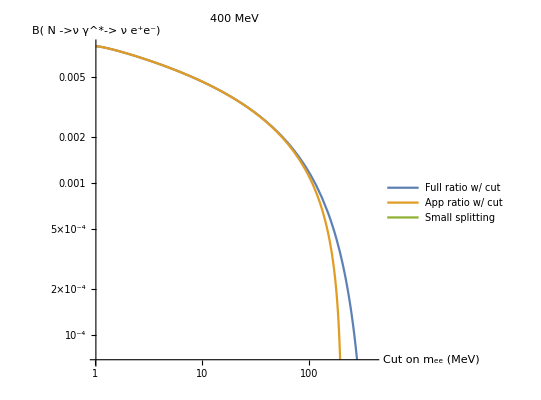

```mathematica
mN = 400;
LogLogPlot[{ratiocut[x/mN,mN],ratiocutapprox[x/mN,mN],ratioCfunction[x/mN,mN]},{x,2*MASSELECTRON,mN}, AxesLabel->{"Cut on m_ee (MeV)","B( N ->ν γ^*-> ν e^+e^-)"},AspectRatio->1,PlotLabel->mN" MeV",PlotLegends->{"Full ratio w/ cut","App ratio w/ cut","Small splitting"}]
```

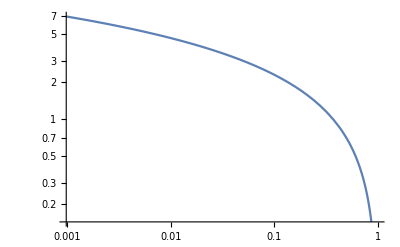

```mathematica
LogLogPlot[Log[1/x],{x,0,1}]
```

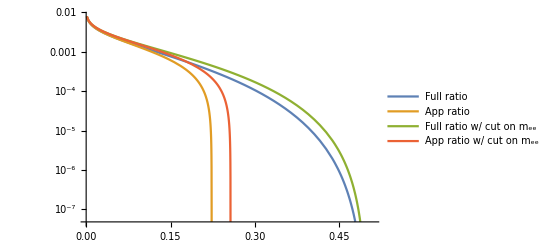

```mathematica
LogPlot[{Gratio[x,mN],Expansion[x,mN],ratiocut[2*x,mN],ratiocutapprox[2*x,mN]},{x,MASSELECTRON/ mN,0.51}, PlotLegends->{"Full ratio","App ratio","Full ratio w/ cut on m_ee","App ratio w/ cut on m_ee"}]
```

```mathematica
MASSMUON=110;
mN=100000000000000000000000;
(16Log[mN/MASSELECTRON]-17)/(16Log[mN/MASSMUON]-17)
Log[mN/MASSELECTRON]/Log[mN/MASSMUON]
```

1.11382

1.11131

## Printing

```mathematica
normalizedfinalgamma
```

-1/(12 π^2)alphaQED dij^2 mh^3 (√(1-4 r^2) (2 r^2-5) r^2+3 √(1-4 r^2)+8 r^6 log((√(1-4 r^2)+1)/(2 r))-2 log((√(1-4 r^2)+1)/r)+log(4))

```mathematica
ToPython[normalizedfinalgamma,"np"]
```

-1/12 * alphaQED * ( dij )**( 2 ) * ( mh )**( 3 ) * ( np.pi )**( -2 ) * ( 3 * ( ( 1 + -4 * ( r )**( 2 ) ) )**( 1/2 ) + ( ( r )**( 2 ) * ( ( 1 + -4 * ( r )**( 2 ) ) )**( 1/2 ) * ( -5 + 2 * ( r )**( 2 ) ) + ( np.log( 4 ) + ( 8 * ( r )**( 6 ) * np.log( 1/2 * ( r )**( -1 ) * ( 1 + ( ( 1 + -4 * ( r )**( 2 ) ) )**( 1/2 ) ) ) + -2 * np.log( ( r )**( -1 ) * ( 1 + ( ( 1 + -4 * ( r )**( 2 ) ) )**( 1/2 ) ) ) ) ) ) )

```mathematica
ToPython[approx3bodycut,"np"]
```

1/36 * alphaQED * ( dij )**( 2 ) * ( mh )**( 3 ) * ( np.pi )**( -2 ) * ( reemin )**( -3 ) * ( 4 * ( r )**( 2 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + ( 5 * ( reemin )**( 2 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + -3 * ( reemin )**( 3 ) * ( 3 + ( 2 * np.log( r ) + ( -1 * np.log( ( reemin + -1 * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) ) ) + np.log( ( reemin + ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) ) ) ) ) ) ) )

```mathematica
Export["full_nuee_dipole.txt",ToPython[normalizedfinalgammacut,"np"]]
```

full_nuee_dipole.txt

```mathematica
normalizedfinalgammacutNOIMAG
```

1/(72 π^2 reemin^3)alphaQED dij^2 mh^3 (reemin^8 (-√(reemin^2-4 r^2))-2 r^2 reemin^6 √(reemin^2-4 r^2)+12 r^4 reemin^4 √(reemin^2-4 r^2)+9 reemin^4 √(reemin^2-4 r^2)-12 r^4 √(1-4 r^2) reemin^3+30 r^2 √(1-4 r^2) reemin^3-18 √(1-4 r^2) reemin^3-36 r^2 reemin^2 √(reemin^2-4 r^2)+10 reemin^2 √(reemin^2-4 r^2)+8 r^2 √(reemin^2-4 r^2)+6 (4 r^6-1) reemin^3 log(√(1-4 r^2)-1)+6 (1-4 r^6) reemin^3 log(√(1-4 r^2)+1)-24 r^6 reemin^3 log(√(reemin^2-4 r^2)-reemin)+6 reemin^3 log(√(reemin^2-4 r^2)-reemin)+24 r^6 reemin^3 log(√(reemin^2-4 r^2)+reemin)-6 reemin^3 log(√(reemin^2-4 r^2)+reemin))

```mathematica
ToPython[normalizedfinalgammacutNOIMAG//TrigExpand//FullSimplify,"np"]
```

1/72 * alphaQED * ( dij )**( 2 ) * ( mh )**( 3 ) * ( np.pi )**( -2 ) * ( reemin )**( -3 ) * ( -6 * ( ( 1 + -4 * ( r )**( 2 ) ) )**( 1/2 ) * ( 3 + ( -5 * ( r )**( 2 ) + 2 * ( r )**( 4 ) ) ) * ( reemin )**( 3 ) + ( 8 * ( r )**( 2 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + ( 2 * ( 5 + -18 * ( r )**( 2 ) ) * ( reemin )**( 2 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + ( 3 * ( 3 + 4 * ( r )**( 4 ) ) * ( reemin )**( 4 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + ( -2 * ( r )**( 2 ) * ( reemin )**( 6 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + ( -1 * ( reemin )**( 8 ) * ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) + 6 * ( -1 + 4 * ( r )**( 6 ) ) * ( reemin )**( 3 ) * ( np.log( ( -1 + ( ( 1 + -4 * ( r )**( 2 ) ) )**( 1/2 ) ) ) + ( -1 * np.log( ( 1 + ( ( 1 + -4 * ( r )**( 2 ) ) )**( 1/2 ) ) ) + ( -1 * np.log( ( -1 * reemin + ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) ) ) + np.log( ( reemin + ( ( -4 * ( r )**( 2 ) + ( reemin )**( 2 ) ) )**( 1/2 ) ) ) ) ) ) ) ) ) ) ) )